## Constants

```mathematica
R=Quantity[8.314,"kg*(meter/second)^2/Kelvin"]
Na=Quantity[6.02*^23,"atoms"]
k=R/Na
mN2=Quantity[28/6.02*^23*.001,"kg/atoms"]
mRb=Quantity[85/6.02*^23*.001,"kg/atoms"]
r1=Quantity[.035/2,"Inches"]
r2=Quantity[.075/2,"Inches"]
totalAperatureArea=UnitConvert[ π(r1^2+r2^2),"cm"]
```

8.314 kg m^2/(s^2 K)

6.02×10^23 atoms

1.38106×10^-23 kg m^2/(s^2 K atoms)

4.65116×10^-26 kg/atoms

1.41196×10^-25 kg/atoms

0.0175 in

0.0375 in

0.0347095 cm^2

## Functions

```mathematica
Zsurface[m_,T_,P_]:=(P^2/(2π m k T))^(1/2);
Zaperature[m_,T_,P_,a_]:=Zsurface[m,T,P]*a;
```

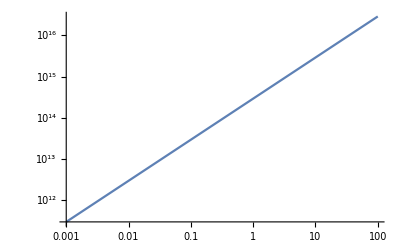

```mathematica
LogLogPlot[Zaperature[mRb,Quantity[273+176,"Kelvins"],Quantity[x*10^12,"atoms/cm^3"]*k*Quantity[273+176,"Kelvins"],totalAperatureArea],{x,.001,100}]
```

## Mean Free Path

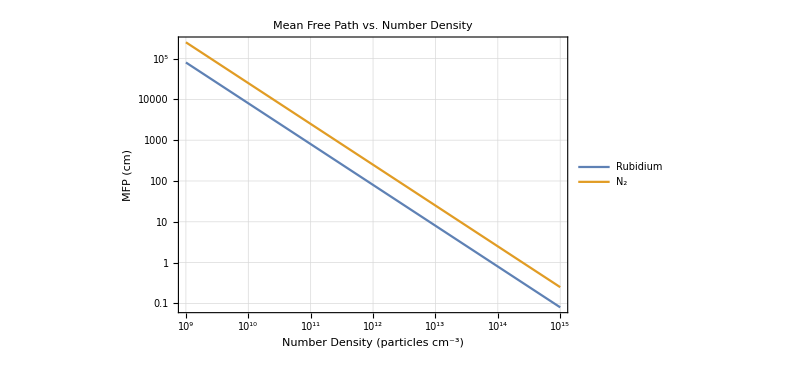

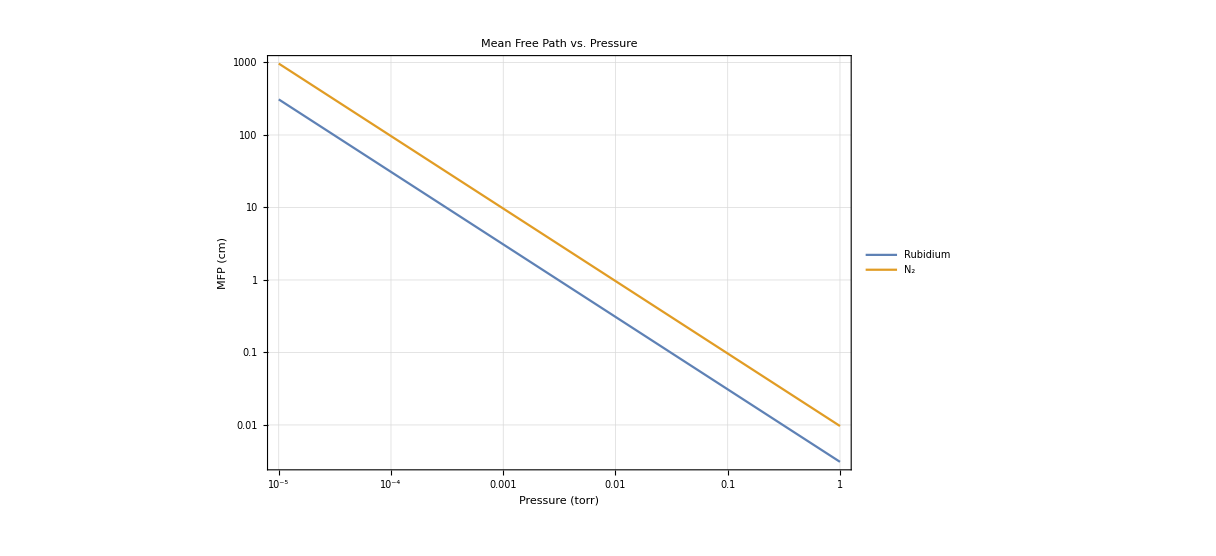

```mathematica
rbDia=2*265*^-10(*centimeters*); (* Actually atomic radius *)
n2Dia=3*^-8(*centimeters*);   (* From BSA *)
nA=6.02*^23(*particles*);
torrToBaryeConv=(1(*atm*))/(760(*torr*))*(1.013*^5(*Pa*))/(1(*atm*))*(10(*barye*))/(1(*Pa*));
meanFreePath[n_,molDia_]:=1/((2)^(.5) n π (molDia)^2);
meanFreePath2[presInTorr_,molDia_, temp_]:=(temp*8.314*^7)/((2)^(.5) presInTorr *nA*torrToBaryeConv*π (molDia)^2);
mfpVsNden=LogLogPlot[{Legended[meanFreePath[n,rbDia],"Rubidium"],Legended[meanFreePath[n,n2Dia],"N_2"]},{n,1*^9,1*^15},PlotRange->Full,LabelStyle->18,GridLines->Automatic,PlotLabel->"Mean Free Path vs. Number Density",FrameLabel->{"Number Density (particles cm^-3)","MFP (cm)"},ImageSize->{600,440},Frame->True]
mfpVsPres=LogLogPlot[{Legended[meanFreePath2[p,rbDia,373],"Rubidium"],Legended[meanFreePath2[p,n2Dia,373],"N_2"]},{p,1*^-5,1},PlotRange->Full,LabelStyle->18,GridLines->Automatic,PlotLabel->"Mean Free Path vs. Pressure",FrameLabel->{"Pressure (torr)","MFP (cm)"},ImageSize->{900,720},Frame->True]
```

## Rb Collisions, low Pressure

```mathematica
rbCollisions=Zsurface[mRb,Quantity[273+176,"Kelvins"],Quantity[1*^10,"atoms/cm^3"]*k*Quantity[273+176,"Kelvins"]];
UnitConvert[rbCollisions,"atoms /cm^2/s"]
Print["Collisions on aperature hole"]
lostParticles=rbCollisions*π*(r1^2+r2^2);
UnitConvert[lostParticles,"atoms/s"]
```

8.36043×10^13 atoms/(cm^2 s)

Collisions on aperature hole

2.90186×10^12 atoms/s

## RbCollisions, high pressure

```mathematica
rbCollisions=Zsurface[mRb,Quantity[273+176,"Kelvins"],Quantity[1*^14,"atoms/cm^3"]*k*Quantity[273+176,"Kelvins"]]
UnitConvert[rbCollisions,"atoms /cm^2/s"]
Print["Collisions on aperature hole"]
lostParticles=rbCollisions*π*(r1^2+r2^2);
UnitConvert[lostParticles,"atoms/s"]
```

8.36043×10^17 atoms/(cm^2 s)

8.36043×10^17 atoms/(cm^2 s)

Collisions on aperature hole

2.90186×10^16 atoms/s

## N_2 Collisions, low pressure

```mathematica
n2Collisions=Zsurface[mN2,Quantity[273+176,"Kelvins"],Quantity[1*^-6*132,"Pascals"]]
UnitConvert[n2Collisions,"atoms /cm^2/s"]
Print["Collisions on aperature hole"]
lostParticles=n2Collisions*π*(r1^2+r2^2);
UnitConvert[lostParticles,"atoms/s"]
```

3.1008×10^18 s Pa atoms/(kg m)

3.1008×10^14 atoms/(cm^2 s)

Collisions on aperature hole

1.07627×10^13 atoms/s

## N_2 Collisions, high pressure

```mathematica
n2Collisions=Zsurface[mN2,Quantity[273+176,"Kelvins"],Quantity[10*132,"Pascals"]];
Print["Collisions per unit area"]
UnitConvert[n2Collisions,"atoms /cm^2/s"]
Print["Collisions on aperature hole"]
lostParticles=n2Collisions*π*(r1^2+r2^2);
UnitConvert[lostParticles,"atoms/s"]
```

Collisions per unit area

3.1008×10^21 atoms/(cm^2 s)

Collisions on aperture hole

1.07627×10^20 atoms/s

## Comparing the collisions at the interface

### Rubidium Collisions

```mathematica
rbCollisions=Zsurface[mRb,Quantity[273+176,"Kelvins"],Quantity[1*^14,"atoms/cm^3"]*k*Quantity[273+176,"Kelvins"]]
UnitConvert[rbCollisions,"atoms /cm^2/s"]
```

8.36043×10^17 atoms/(cm^2 s)

8.36043×10^17 atoms/(cm^2 s)

### Nitrogen Collisions

```mathematica
n2Collisions=Zsurface[mN2,Quantity[273+176,"Kelvins"],Quantity[.0002*132,"Pascals"]]
UnitConvert[n2Collisions,"atoms /cm^2/s"]
```

6.20159×10^20 s Pa atoms/(kg m)

6.20159×10^16 atoms/(cm^2 s)